```mathematica
(* we shall work with 2^n sites *)
n=4;
```

```mathematica
(* add a "0" to the left of string s *)
joinLeft[s_]:=StringInsert[s,"0",1];
(* add a "1" to the left of string s *)
joinRight[s_]:=StringInsert[s,"1",1];
(* generate next string from the previous one *)
iter[s_]:=Join[joinLeft@s,joinRight@Reverse[s]];
```

```mathematica
(* list of positions for the length 2^4 chain *)
l=Nest[iter,{"0","1"},n-1]
(* list of positions in the atomic base *)
l=FromDigits[#,2]&/@l
(* and back to base 2 *)
BaseForm[%,2]
```

{0000,0001,0011,0010,0110,0111,0101,0100,1100,1101,1111,1110,1010,1011,1001,1000}

{0,1,3,2,6,7,5,4,12,13,15,14,10,11,9,8}

{0_2,1_2,11_2,10_2,110_2,111_2,101_2,100_2,1100_2,1101_2,1111_2,1110_2,1010_2,1011_2,1001_2,1000_2}

```mathematica
n=3
Nest[iter,{"0","1"},n-1]
```

3

{000,001,011,010,110,111,101,100}

```mathematica
2^4
```

16

```mathematica
(* atomica basis of localized states *)
loc=IdentityMatrix[2^n];
(* hash table connecting localized states (atomic basis) to the reordering of the basis *)
ht=<|Table[l[[i]]->loc[[i]],{i,2^n}]|>
(*GraphPlot[ht,VertexLabeling->True]*)
```

<|0→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1→{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},3→{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},2→{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},6→{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},7→{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},5→{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},4→{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},12→{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},13→{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},15→{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},14→{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},10→{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},11→{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},9→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},8→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}|>

```mathematica
(* bitwise scalar product *)
scal[b1_,b2_]:=Plus@@IntegerDigits[BitAnd[b1,b2],2];
```

```mathematica
(* check *)
i=11;j=16;
BaseForm[#,2]&/@{l[[i]],l[[j]]}
scal[l[[i]],l[[j]]]
```

{1111_2,1000_2}

1

```mathematica
(* eigenstates at first order in the couplings between neighbouring sites *)
(* b is the binary index of the associated energy, with the following convention: ϵ=(-1)^Subscript[b, 1] Subscript[t, 1]+(-1)^Subscript[b, 2] Subscript[t, 2]/2+..(-1)^Subscript[b, n] Subscript[t, n]/2^(n-1) --> b=Subscript[b, n]... Subscript[b, 2] Subscript[b, 1] *)
val[b_]:=Sum[(-1)^(IntegerDigits[b,2,n][[n+1-it]])t[it]/2^(it-1),{it,n}]
vec[b_]:=2^(-n/2)Sum[(-1)^scal[z,b] ht[z],{z,0,2^n-1}]
```

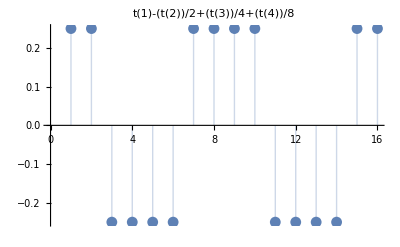

```mathematica
bb=2;
ListPlot[vec[bb],Filling->Axis,PlotLabel->val[bb]]
```

```mathematica
vec[3]
```

{1/4,-1/4,1/4,-1/4,-1/4,1/4,-1/4,1/4,0,0,0,0,0,0,0,1/4}